# Plot Testi di S. Berardi, M. Grangetto e M. Billo’ Basato sulle dispense di Laboratorio di Calcolo I del 1998-2007 e di TIF del 2008-2011

Creare grafici di funzioni.

 Il comando Plot[f[x],{x,a,b}] disegna il grafico di f[x] tra x=a ed x=b. La forma più generale del comando è 
                      Plot[f[x],{x,a,b}, opzione_1->valore_1, ..., opzione_n -> valore_n] 
Le “opzioni” sono scelte di modi con cui stampare un grafico. Ogni opzione ha diversi valori possibili, corrispondenti a diverse scelte. Normalmente ogni opzione ha un valore di default, ma scrivendo opzione -> valore entro Plot[...] possiamo assegnarle temporaneamente un valore diverso. Vedremo ora diversi esempi di opzioni, che ci consentono di stampare un grafico con le caratteristiche desiderate. 
Come prima prova disegnamo sin(x) per x tra 0 e 2π.

```mathematica
Options[Plot]
```

```mathematica
Plot[Sin[x],{x,0,2 Pi}]
```

È possibile assegnare un nome a una funzione ed utilizzare il nome in Plot.

```mathematica
FF= Sin[x]^2 -3x
Plot[FF,{x,0,10}]
```

2. PlotRange. 
PlotRange->{c,d} fa disegnare i soli valori della y compresi tra c e d: dunque disegna solo la parte del grafico tra le due rette orizzontali y=c ed y=d. 
Ridisegnare sin(x) per x tra 0 e 2π, e per y tra -0.5 e 0.5.

```mathematica
Plot[Sin[x],{x,0,2π},PlotRange->{-0.5, 0.5}]
```

3. AspectRatio->x. 
Rende l’altezza del disegno pari a x volte la base. Se x=1 il disegno diventa quadrato. Tuttavia, la scala sugli assi x e y può essere diversa: infatti la forma quadrata o rettangolare del disegno non ha nulla a che vedere con la scala usata sui due assi.
Ridisegnare sin(x) entro un quadrato e con la larghezza del grafico pari a tre volte l’altezza.

```mathematica
Plot[Sin[x],{x,0,2Pi},AspectRatio->1]
```

```mathematica
Plot[Sin[x],{x,0,2 Pi},AspectRatio->1/3]
```

4. Stessa scala negli assi x e y. 
Per avere la stessa scala sui due assi occorre scegliere AspectRatio -> Automatic. Il rapporto tra base e altezza della figura viene scelto di conseguenza.
ImageSize determina la larghezza del disegno in pixels
Ridisegnare sin(x) in un rettangolo [-10,10]x[-5,5], usando la stessa scala per x e y .

```mathematica
Plot[Sin[x],{x,-10,10},AspectRatio -> Automatic,PlotRange->{-5,5}, ImageSize-> 800]
```

4bis. Per comprendere meglio cosa avviene a seconda se chiediamo oppure no la stessa scala sui due assi, disegnare la funzione Sqrt[1-x^2], per x nell’intervallo [-1,1], che rappresenta un arco di circonferenza, prima senza specificare alcuna opzione, e poi specificando AspectRatio->Automatic

```mathematica
Plot[Sqrt[1-x^2],{x,-1,1}]
```

```mathematica
Plot[Sqrt[1-x^2],{x,-1,1},AspectRatio->Automatic]
```

5. Colori. 
L’opzione PlotStyle si puo’ usare per assegnare un particolare colore alla curva. Mathematica ha una serie di colori predefiniti: Red, Blue, Yellow, Green, ... (indicati dal loro nome con la prima lettera maiuscola). Provare a fare un grafico di una funzione con l’opzione PlotSytle->un colore.

```mathematica
Plot[Sin[x],{x,-10,10},PlotStyle-> Red]
```

5bis. Si possono creare colori personalizzati con la funzione RGBColor[r,g,b], che crea la mistura di r parti di red (rosso), g parti di green (verde), b parti di blue (blu). r,g,b sono valori tra 0 e 1. 
Altre funzioni disponibili sono CMYKColor[c,m,y,k], che fornisce una mistura dei colori primari definiti invece “per sottrazione” da uno sfondo bianco  (cyan, magenta, yellow, black), GrayLevel[g], che fornisce una gradazione di grigio. Provare a definire alcuni colori: red, green, blue, ... , mescolando i colori rosso, verde e blu in diverse proporzioni, e usando RGBColor. Dovrete usarli in un disegno per vedere come sono, la definizione astratta non e’ di grande aiuto.

```mathematica
red          = RGBColor[1,0,0]
green      = RGBColor[0,1,0]
blue        = RGBColor[0,0,1]
cyan        = CMYKColor[1,0,0,0] (* "cyan" o "color cianuro" è l'azzurro *)
magenta = CMYKColor[0,1,0,0]
yellow    = CMYKColor[0,0,1,0]
black      = CMYKColor[0,0,0,1]
gray        = GrayLevel[0.8]
```

6.Grafici di più funzioni. 
Per i grafici di più funzioni con dei colori voluti, è sufficiente fornire a Plot la lista di funzioni da disegnare. Disegnate il grafico di sin(x), cos(x), tan(x) in colori diversi (è sufficiente assegnare a PlotStyle la lista {col_1, ..., col_n} dei colori). Se non precisiamo qualii colori usare per ogni funzione, Mathematica li sceglie al posto nostro.

```mathematica
Plot[{Sin[x],Cos[x],Tan[x]},{x,0,2*Pi},PlotStyle->{red,green,blue}]
Plot[{Sin[x],Cos[x],Tan[x]},{x,0,2*Pi}]
```

```mathematica
A ={Brown,Orange,Pink} (* colori definiti internamente a Mathematica *)
Table[Plot[Sin[x],{x,-10,10},PlotStyle-> A[[i]]],{i,1,3}]
```

7.Come viene costruito il grafico? 
Per disegnare un grafico il comando Plot valuta la funzione su nun numero limitato di punti; il grafico prodotto e’ frutto di interpolazione (ogni punto viene collegato al successivo da un opportuno arco di parabola), e non sempre permette di ottenere il risultato desiderato. L’opzione Mesh->All permette di mostrare i punti in cui la funzione viene valutata. L’opzione PlotPoints si puo’ usare per fissare il numero di punti iniziali su cui valutare la funzione (tuttavia, Mathematica in seguito ne aggiunge altri per migliorare il disegno, a meno che chiediamo MaxRecursion->1). 
Provare a disegnare le funzioni Sin[x] e Sin[1/x] con le opzioni PlotPoints->100, Mesh->All, MaxRecursion->1. Nel caso Sin[1/x] provare anche con PlotPoints->10.

```mathematica
Plot[Sin[x],{x,-Pi,Pi},Mesh->All,PlotPoints-> 10] (* ai 10 punti iniziali Mathematica ne aggiunge altri la' dove la precisione del disegno lo richiede *)
```

```mathematica
Plot[Sin[1/x],{x,-2,2},Mesh->All, PlotPoints->100,MaxRecursion->1]
(* i punti usati sono 100 e non se ne aggiungono altri. Di conseguenza in alcuni punti la precisione del grafico lascia a desiderare. *)
```

8. Origine degli assi.
 L’opzione AxesOrigin->{x,y} permette di fissare l’origine degli assi alle coordinate (x,y).  Disegnare la funzione 2 (x - 4)^2 + 1 prima senza scegliere l’origine, e poi fissando l’origine in (0,0).

```mathematica
Plot[2  (x-4)^2+1,{x,3,5}]
```

```mathematica
Plot[2  (x-4)^2+1,{x,3,5}, AxesOrigin->{0,0}]
```

9. Griglia degli assi.  
Le opzioni GridLines e e GridLinesStyle si possono usare per aggingere una griglia quadrettata al grafico.

```mathematica
Plot[Sin[x]^2,{x,0,2 Pi},GridLines-> Automatic, GridLinesStyle->Dashed]
```

```mathematica
Plot[Sin[x]^2,{x,0,2 Pi},GridLines-> {{0,Pi/2,Pi,3 Pi/2 ,2 Pi},{0,0.25,0.5,0.75,1}}, GridLinesStyle->Dashed]
```

Ottenere lo stesso risultato usando Range oppure Table per specificare la posizione della linee della griglia.

10. Ticks.
L’opzione Ticks (ovvero “tacche”) si puo’ usare per scegliere i punti in cui mostrare le tacche degli assi.

```mathematica
Plot[Sin[x]^2,{x,0,2 Pi},Ticks->{{0, Pi , 2 Pi},{0, 0.5,1}}]
(* la prima lista di valori si riferisce alla x, la seconda alla y *)
```

11. AxesLabel. 
L’opzione AxesLabel->{stringa_x, stringa_y} aggiunge le etichette testuali agli assi.

```mathematica
Plot[Sin[x]^2,{x,0,2 Pi},AxesLabel->{x,Sin[x]^2}]
```

12. Altre opzioni utili.

Directive, PlotLegends, Fiiling

```mathematica
Plot[{Sin[x],Cos[x]},{x,0,2 Pi}, Ticks->{Range[0,2 Pi, Pi/2],Range[0,1,0.25]},PlotStyle->{Directive[Red,Dashed], RGBColor[0,0.5, 0]},AxesLabel->{x,y},
PlotLegends->"Expressions"]
```

```mathematica
Plot[{Sin[x],Cos[x]},{x,0,2 Pi}, Ticks->{Range[0,2 Pi, Pi/2],Range[0,1,0.25]},PlotStyle->{Directive[Red,Dashed,Thick], RGBColor[0,0.5, 0]},AxesLabel->{x,y},
PlotLegends-> {"sin(x)","Cos(X)"}]
```

```mathematica
Plot[{Sin[x],Cos[x]},{x,0,2 Pi}, Ticks->{Range[0,2 Pi, Pi/2],Range[0,1,0.25]},PlotStyle->{Directive[Red,DotDashed], RGBColor[0,0.5, 0]},AxesLabel->{x,y},
PlotLegends-> Placed[{"sin(x)","Cos(XY)"},Above]]
(* RGBColor[0,0.5,0] e' una media tra RGBColor[0,0,0] (il nero) e RGBColor[0,1,0] il verde.Corrisponde quindi al verde scuro *)
```

```mathematica
Plot[2*x*Sin[x],{x,0,15},Filling->Top]
```

```mathematica
Plot[2*x*Sin[x],{x,0,15},Filling->Bottom]
```

```mathematica
Plot[2*x*Sin[x],{x,0,15},Filling->Axis]
```

Plot logaritmici

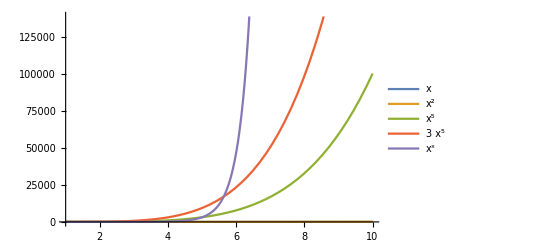

```mathematica
Plot[{x,x^2,x^5,3x^5,x^x},{x,1,10},PlotLegends->"Expressions"]
```

Se le funzioni sono sempre positive si può usare un plot logaritmico.
Log[ax] = Log[a]+Log[x]: Curve legate da una costante di proporzionalità appaiono con differenza costante in
plot logaritmico. Asse y è fortemente compresso

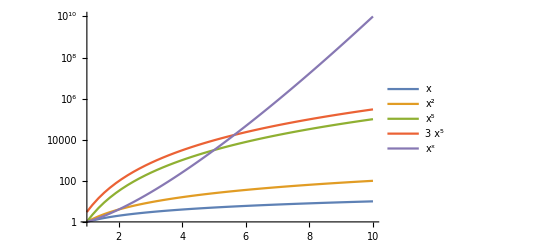

```mathematica
LogPlot[{x,x^2,x^5,3 x^5,x^x},{x,1,10},PlotLegends->"Expressions"]
```

Se le funzioni e il range sono sempre positivi si può usare un plot doppio logaritmico.
Se y = x^b   Log[y] = b Log[x]: Curve con andamento a potenza appaiono come linee rette in un plot
doppio logaritmico. Sia l’asse x che l’asse y sono fortemente compressi.

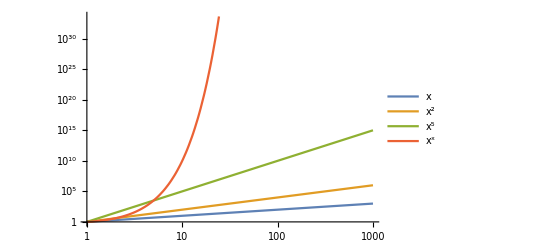

```mathematica
LogLogPlot[{x,x^2,x^5,x^x},{x,1,1000},PlotLegends->"Expressions"]
```